```mathematica
boxlength = 1.5;
halfwidth = 0.05;
σ=halfwidth/Sqrt[2Log[2]];
Δx=0.02;
Δt=0.01;
tmax=3;
x0=0.7;
barrierwidth=0.2;
k0=50Pi;
V0=2(50Pi)^2;
E0 = (50Pi)^2;
α=I Δt/(4(Δx)^2);
```

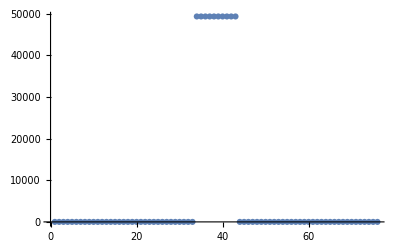

```mathematica
psi[x_,0]=Exp[I k0 x]Exp[-(x-x0)^2/(2σ^2)] ;
psilist={};
psi0=Table[psi[x,0],{x,0,boxlength,Δx}];
AppendTo[psilist,psi0];
V=Table[V0*HeavisideTheta[x-((boxlength-barrierwidth)/2)]HeavisideTheta[((boxlength+barrierwidth)/2)-x],{x,0,boxlength,Δx}];
β=Table[I Δt/2(1/(Δx)^2+V[[i]]),{i,1,Length[V]}];
ListPlot[V]
```

```mathematica
D1=Table[0,{i,1,boxlength/Δx+1},{j,1,boxlength/Δx+1}];
D2=Table[0,{i,1,boxlength/Δx+1},{j,1,boxlength/Δx+1}];
```

```mathematica
For[i=1,i≤boxlength/Δx+1,i++,If[i==1,D1[[i,i]]=1-β[[i]];D1[[i,i+1]]=α,If[i==Floor[boxlength/Δx+1],D1[[i,i-1]]=α;D1[[i,i]]=1-β[[i]],D1[[i,i-1]]=α;D1[[i,i]]=1-β[[i]];D1[[i,i+1]]=α]]]
For[i=1,i≤boxlength/Δx+1,i++,If[i==1,D2[[i,i]]=1+β[[i]];D2[[i,i+1]]=-α,If[i==Floor[boxlength/Δx+1],D2[[i,i-1]]=-α;D2[[i,i]]=1+β[[i]],D2[[i,i-1]]=-α;D2[[i,i]]=1+β[[i]];D2[[i,i+1]]=-α]]]
```

```mathematica
D2inv=PseudoInverse[D2]
```

{{0.0333688-0.115641 ⅈ,0.048235-0.0766211 ⅈ,0.0508419-0.0453187 ⅈ,0.0461977-0.0221511 ⅈ,0.0380094-0.00637506 ⅈ,0.0288011+0.00331944 ⅈ,64,-1.84981×10^-19-1.01824×10^-19 ⅈ,1.98905×10^-19-2.97067×10^-20 ⅈ,-9.61166×10^-20+8.70138×10^-20 ⅈ,5.60874×10^-20-1.2286×10^-20 ⅈ,-8.12824×10^-20-1.68138×10^-19 ⅈ,7.89456×10^-20+1.86686×10^-19 ⅈ},74,{1}}
 |  |  |  |

```mathematica
For[t=0,t<=tmax,t=t+Δt,AppendTo[psilist,D2inv.D1.(psilist[[ Length[psilist]]])]]
```

{1}
 |  |  |  |

103

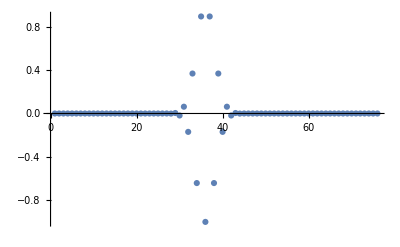

```mathematica
ListPlot[Re[psilist][[1]],PlotRange->All]
```

```mathematica
Length[psilist]
```

302

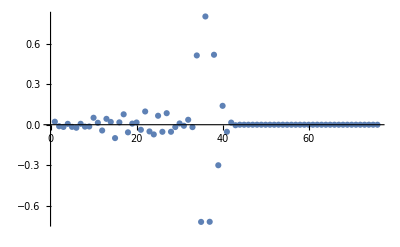

```mathematica
ListPlot[Im[psilist][[300]],PlotRange->All]
```

```mathematica
ListPlot3D[Re[psilist],PlotRange->All]
```

-Graphics3D-